```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]==3&&IsomorphicGraphQ[VertexDelete[g,{4,5}],CompleteGraph[3]]]&]
```

{26487}

```mathematica
allGraphs5[26487,"graph"]
```

-Graphics-

```mathematica
VertexDelete[allGraphs6[7164612,"graph"],{4,5,6}]
```

-Graphics-

```mathematica
Sort [Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[allGraphs5[26487,"colofour"]]]]]
```

{{2,9},{3,7},{4,1}}

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5 && EdgeCount[g]== Binomial[4,2] &&IsomorphicGraphQ[VertexDelete[g,{5}],CompleteGraph[4]]]&]
```

{28764}

```mathematica
allGraphs5[28764,"graph"]
```

-Graphics-

```mathematica
Sort [Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[allGraphs5[28764,"colofour"]]]]]
```

{{3,4},{4,1}}

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6 && EdgeCount[g]==3&&IsomorphicGraphQ[VertexDelete[g,{4,5,6}],CompleteGraph[3]]]&]
```

{6396975}

```mathematica
Sort [Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[allGraphs6[6396975,"colofour"]]]]]
```

{{2,27},{3,37},{4,12},{5,1}}

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6 && EdgeCount[g]==6&&IsomorphicGraphQ[VertexDelete[g,{5,6}],CompleteGraph[4]]]&]
```

{6935220}

```mathematica
Sort [Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[allGraphs6[6935220,"colofour"]]]]]
```

{{3,16},{4,9},{5,1}}

```mathematica
FormulaSummary[all_,key_]:=Sort [Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[all[key,"colofour"]]]]]
```

```mathematica
With[
{all=allGraphs6,max=6},
TableForm[
Table[
With[
{key=First[Select[Keys[all],With[{g=all[#,"graph"]},
VertexCount[g]==max && EdgeCount[g]==Binomial[k,2]&&
IsomorphicGraphQ[
With[{remove=Range[k+1,max]},
If[remove=={},
g,
VertexDelete[g,remove]
]
],CompleteGraph[k]]
]&]]},
Map[Last,FormulaSummary[all,key]]
]
,
{k,1,max}]
]
]
```

1 | 31 | 90 | 65 | 15 | 1
16 | 65 | 55 | 14 | 1 | 
27 | 37 | 12 | 1 |  | 
16 | 9 | 1 |  |  | 
5 | 1 |  |  |  | 
1 |  |  |  |  |

```mathematica
With[
{all=allGraphs5,max=5},
TableForm[
Table[
With[
{key=First[Select[Keys[all],With[{g=all[#,"graph"]},
VertexCount[g]==max && EdgeCount[g]==Binomial[k,2]&&
IsomorphicGraphQ[
With[{remove=Range[k+1,max]},
If[remove=={},
g,
VertexDelete[g,remove]
]
],CompleteGraph[k]]
]&]]},
Map[Last,FormulaSummary[all,key]]
]
,
{k,1,max}]
]
]
```

1 | 15 | 25 | 10 | 1
8 | 19 | 9 | 1 | 
9 | 7 | 1 |  | 
4 | 1 |  |  | 
1 |  |  |  |

## Now more direct without tables

```mathematica
FindFullFormula[Graph[{1,2,3},{}],Table[{k},{k,1,3}]]
```

{v1x2x3,v1x23,v13x2,v12x3,v312}

```mathematica
FormulaSummary2[form_]:=Sort [Tally[Map[StringCount[SymbolName[#],"x"]&,ListofVars[form]]]]
```

```mathematica
With[
{max=11},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[max],Subsets[Range[kk],{2}],VertexLabels->"Name"]},
PadLeft[
Map[Last,FormulaSummary2[FindFullFormula[g,Table[{j},{j,1,max}]]]],
max+1]
]
,
{kk,1,max}],
kk],
TableHeadings->{Range[max],Range[max+1]}
]
]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
1 | 0 | 1 | 1023 | 28501 | 145750 | 246730 | 179487 | 63987 | 11880 | 1155 | 55 | 1
2 | 0 | 0 | 512 | 19171 | 111645 | 204205 | 156660 | 58107 | 11130 | 1110 | 54 | 1
3 | 0 | 0 | 0 | 6561 | 58975 | 133057 | 116298 | 47271 | 9702 | 1022 | 52 | 1
4 | 0 | 0 | 0 | 0 | 16384 | 61741 | 70035 | 33621 | 7770 | 896 | 49 | 1
5 | 0 | 0 | 0 | 0 | 0 | 15625 | 31031 | 19981 | 5590 | 740 | 45 | 1
6 | 0 | 0 | 0 | 0 | 0 | 0 | 7776 | 9031 | 3465 | 565 | 40 | 1
7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2401 | 1695 | 385 | 34 | 1
8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 512 | 217 | 27 | 1
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 81 | 19 | 1
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10 | 1
11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

```mathematica
With[
{max=12},
TableForm[
Monitor[
Table[
With[
{g=Graph[Range[max],Subsets[Range[kk],{2}],VertexLabels->"Name"]},
PadLeft[
Map[Last,FormulaSummary2[FindFullFormula[g,Table[{j},{j,1,max}]]]],
max+1]
]
,
{kk,1,max}],
kk],
TableHeadings->{Range[max],Range[max+1]}
]
]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
1 | 0 | 1 | 2047 | 86526 | 611501 | 1379400 | 1323652 | 627396 | 159027 | 22275 | 1705 | 66 | 1
2 | 0 | 0 | 1024 | 58025 | 465751 | 1132670 | 1144165 | 563409 | 147147 | 21120 | 1650 | 65 | 1
3 | 0 | 0 | 0 | 19683 | 242461 | 724260 | 830845 | 447195 | 124887 | 18900 | 1542 | 63 | 1
4 | 0 | 0 | 0 | 0 | 65536 | 325089 | 481951 | 305382 | 95781 | 15834 | 1386 | 60 | 1
5 | 0 | 0 | 0 | 0 | 0 | 78125 | 201811 | 170898 | 64701 | 12250 | 1190 | 56 | 1
6 | 0 | 0 | 0 | 0 | 0 | 0 | 46656 | 70993 | 36751 | 8550 | 965 | 51 | 1
7 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16807 | 15961 | 5160 | 725 | 45 | 1
8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4096 | 2465 | 487 | 38 | 1
9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 729 | 271 | 30 | 1
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 100 | 21 | 1
11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 11 | 1
12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1

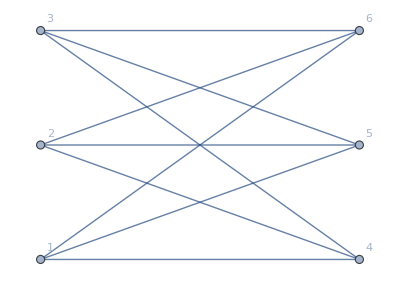

```mathematica
g=Graph[CompleteGraph[{3,3}],VertexLabels->"Name"]
```

```mathematica
FindFullFormula[CompleteGraph[{3,3}],Table[{k},{k,1,6}]]
```

{v1x2x3x4x5x6,v1x2x3x4x56,v1x2x3x46x5,v1x2x3x45x6,v1x2x3x645,v1x23x4x5x6,v1x23x4x56,v1x23x46x5,v1x23x45x6,v1x23x645,v13x2x4x5x6,v13x2x4x56,v13x2x46x5,v13x2x45x6,v13x2x645,v12x3x4x5x6,v12x3x4x56,v12x3x46x5,v12x3x45x6,v12x3x645,v312x4x5x6,v312x4x56,v312x46x5,v312x45x6,v312x645}

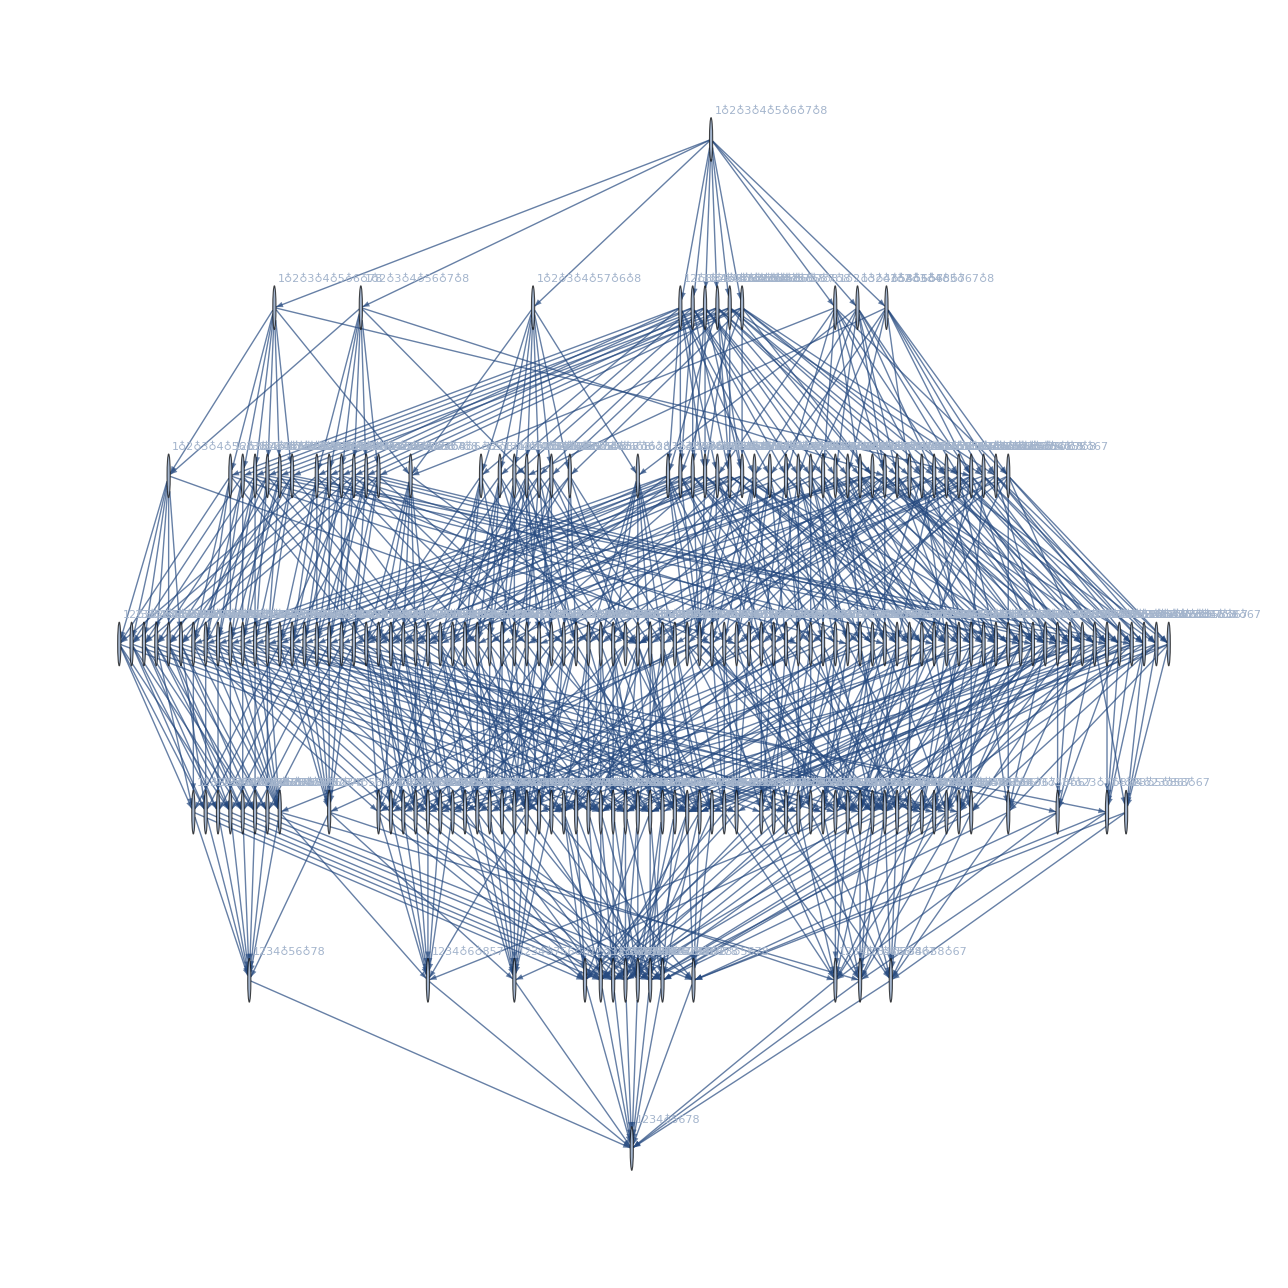

```mathematica
FormulaGraph[FindFullFormula[CompleteGraph[{4,4}],Table[{k},{k,1,8}]]]
```

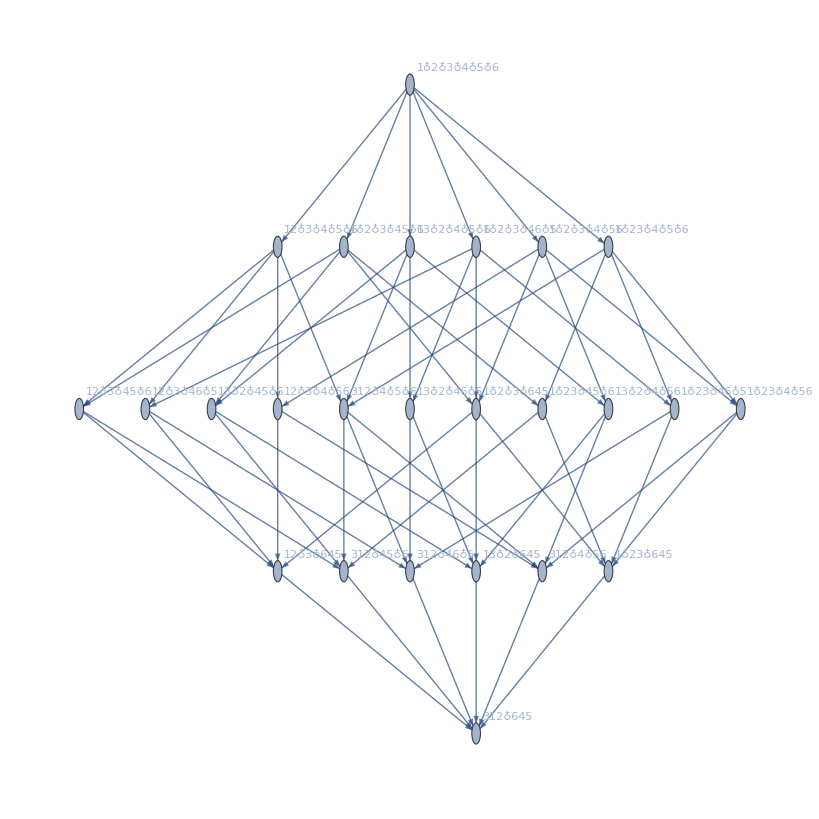

```mathematica
FormulaGraph[FindFullFormula[CompleteGraph[{3,3}],Table[{k},{k,1,6}]]]
```

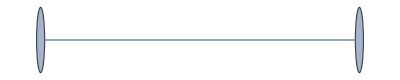
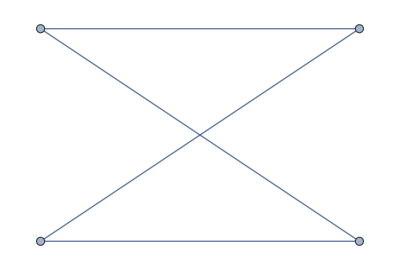
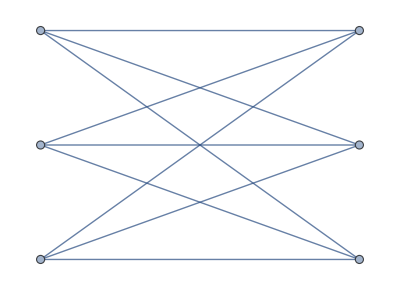

```mathematica
Table[CompleteGraph[{max,max}],{max,1,3}]
```

```mathematica
TableForm[Table[Map[Last,FormulaSummary2[FindFullFormula[CompleteGraph[{Ceiling[max/2],Floor[max/2]}],Table[{k},{k,1,max}]]]],{max,1,5}],TableDepth->2]
```

CompleteGraph::ilsmp: Single or list of positive machine-sized integers expected at position 1 of CompleteGraph[{1, 0}].

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[CompleteGraph[{1,0}]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[CompleteGraph[{1,0}]]].

Part::partw: Part 2 of GraphComplement[CompleteGraph[{1,0}]] does not exist.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

Part::pkspec1: The expression pos2 cannot be used as a part specification.

Part::pkspec1: The expression pos1 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]].

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]]].

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]]]].

Part::partw: Part 2 of GraphComplement[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]]] does not exist.

Set::pkspec1: The expression pos1 cannot be used as a part specification.

Delete::pkspec: The expression pos2 cannot be used as a part specification. Use Key[pos2] instead.

EdgeAdd::graph: A graph object is expected at position 1 in EdgeAdd[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]],GraphComplement[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]]]].

GraphComplement::graph: A graph object is expected at position 1 in GraphComplement[EdgeAdd[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]],GraphComplement[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]]]]].

General::stop: Further output of GraphComplement::graph will be suppressed during this calculation.

EdgeList::graph: A graph object is expected at position 1 in EdgeList[GraphComplement[EdgeAdd[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]],GraphComplement[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{«2»}]]]]]]].

General::stop: Further output of EdgeList::graph will be suppressed during this calculation.

Part::partw: Part 2 of GraphComplement[EdgeAdd[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]],GraphComplement[EdgeAdd[CompleteGraph[{1,0}],GraphComplement[CompleteGraph[{1,0}]]]]]] does not exist.